## 167Ta

```mathematica
ClearAll["Global`*"]
```

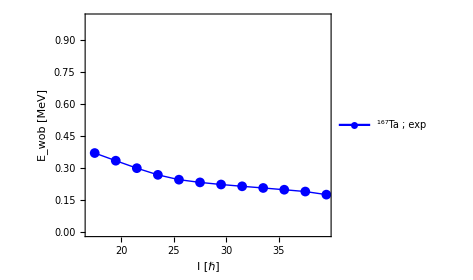

```mathematica
yrastEn=Sort[{13343.4,12240.4,11200.4,10213.8,9280.0,8398.6,7565.8,6779.9,6035.6,5326.2,4661.0,4045.2,3480.2,2962.8,2477.37,2056.96}];
wob1En=Sort[{12968.0,11910.9,10906.1,9954.1,9054.3,8205.6,7406.1,6653.7,5949.4,5293.3,4687.7,4133.1}];
yrastSpin=Table[i/2,{i,21,81,4}];
wob1Spin=Table[i/2,{i,35,79,4}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i+3]]+yrast[[i+4]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black},PlotLegends->Placed[{Style[Row[{Superscript["","167"],"Ta ; exp"}],30]},{0.4,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/167Ta.pdf",fig];
Show[fig]
```